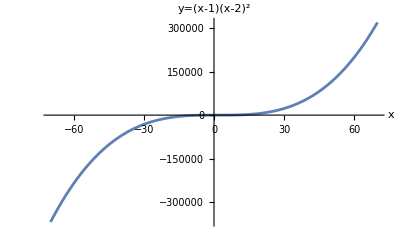

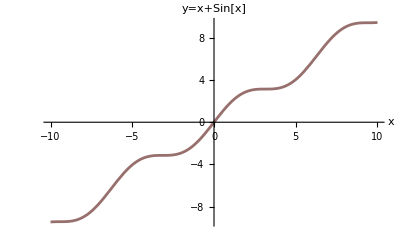

```mathematica
Plot[(x-1)(x-2)^2,{x,-70,70},AxesLabel->{"x","y=(x-1)(x-2)^2"},PlotPoints->100]
Plot[x+Sin[x],{x,-10,10},AxesLabel->{"x","y=x+Sin[x]"},ColorFunction->"Rainbow"]
```

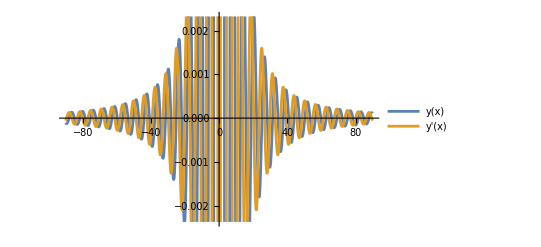

```mathematica
y[x_]:=Sin[x]/(1+x^2)
Plot[{y[x],y'[x]},{x,-90,90},PlotLegends->"Expressions"]
```

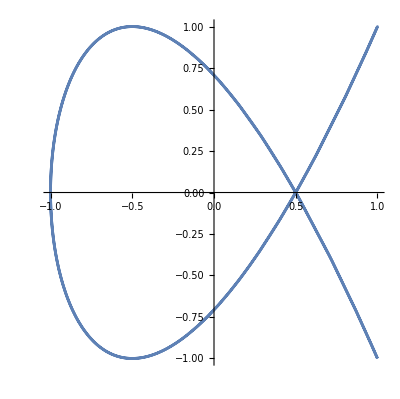

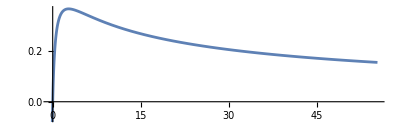

```mathematica
a=1;
ParametricPlot[{a Cos[2t],a Cos[3t]},{t,-π,π}]
ParametricPlot[{t Log[t],Log[t]/t},{t,0,6π},AspectRatio->1/3]
```

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-3,3},{y,-3,3}]
Plot3D[Sin[x+Cos[y]],{x,-6,6},{y,-6,6}]
Plot3D[(x^2-y^2)/(x^3+y^3),{x,-10,10},{y,-10,10}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},2<x^2+y^2<3]]
Plot3D[1/(y^2-x^3+3x-3),{x,-3,3},{y,-3,3},RegionFunction->Function[{x,y},0<Mod[x^2+y^2,2]<1],PlotPoints->100]
```

-Graphics3D-

-Graphics3D-